```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Decay length of Neutral Pion

```mathematica
ReplaceAll[γ*β*τ/.γ->1/Sqrt[1-β^2],β->(√ϵ √(2 m+ϵ))/(m+ϵ)]//FullSimplify
```

```mathematica
d=Convert[(√ϵ √(2 m+ϵ) τ)/(√(m^2/(m+ϵ)^2) (m+ϵ))*SpeedOfLight/.{τ->9*10^-17 Second,m->140 Mega ElectronVolt,ϵ->ϵ Mega ElectronVolt}//FullSimplify,Centimeter];
```

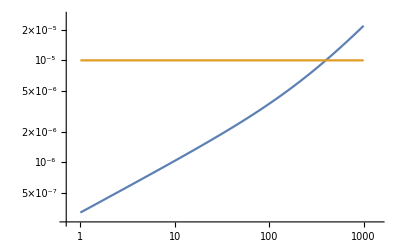

```mathematica
LogLogPlot[{d 1/Centimeter,10^-5},{ϵ,1,10^3}]
```